```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/neupackage/mma/package-test

```mathematica
Get["../dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Define Beams

```mathematica
NBeamsLR[4]
```

{{-π/2,0.451027},{-π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

```mathematica
spectDBWC1={{1,-0.6},{1,0.6}}
spectDBWC2={{0.5,-0.6},{1,0.6}}
spectDBWC3={{0.1,-0.6},{1,0.6}}
```

{{1,-0.6},{1,0.6}}

{{0.5,-0.6},{1,0.6}}

{{0.1,-0.6},{1,0.6}}

```mathematica
spectDBC1={{-1,-0.6},{1,0.6}}
spectDBC2={{-0.5,-0.6},{1,0.6}}
spectDBC3={{-0.1,-0.6},{1,0.6}}
```

{{-1,-0.6},{1,0.6}}

{{-0.5,-0.6},{1,0.6}}

{{-0.1,-0.6},{1,0.6}}

## Define Useful Functions

```mathematica
DBPltDR[spect_]:=Module[{spectM},

spectM=spect;

ParametricPlot[
{DBAxialSymKNMAA[spectM, n],DBAxialSymOmegaNMAA[spectM, n]},
{n,-20,20},
PlotRange->{{-2,2},{-2,2}},
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltOmegaN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymOmegaNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"ω(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltKN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymKNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"k(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

## Calculate DR

Test Functions

```mathematica
DBAxialSymIntFun0n[spectDBC2,n]
DBAxialSymIntFun1n[spectDBC2,n]
DBAxialSymIntFun2n[spectDBC2,n]
```

1/(1-0.6 n)-0.5/(1+0.6 n)

0.6/(1-0.6 n)+0.3/(1+0.6 n)

0.36/(1-0.6 n)-0.18/(1+0.6 n)

```mathematica
DBAxialSymOmegaNMAA[spectDBC1, n]
```

1/4 (0.64/(1-0.6 n)-0.64/(1+0.6 n))

```mathematica
DBAxialSymKNMAA[spectDBC1, n]
```

1/4 (0.64/(1-0.6 n)-0.64/(1+0.6 n)) n

Compare with the previous functions

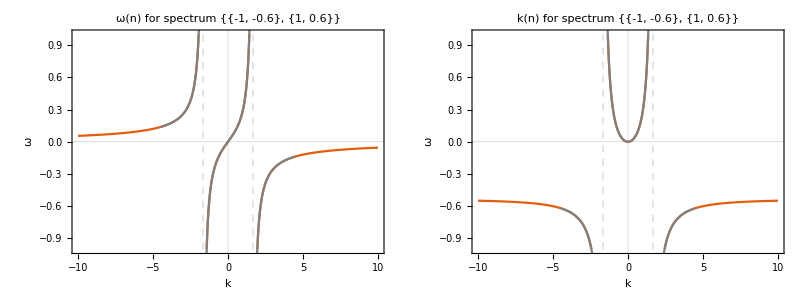

```mathematica
Grid@{{
Show[
DBPltOmegaN[spectDBC1],
NBeamsOmegaNPlt[spectDBC1]
],
Show[
DBPltKN[spectDBC1],
NBeamsKNPlt[spectDBC1]
]
}}
```

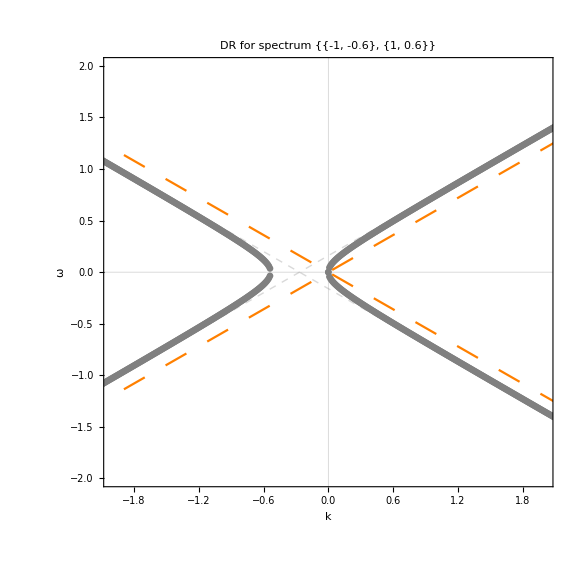

```mathematica
Show[
DBPltDR[spectDBC1],NBeamsOmegaKPlt[spectDBC1][[2]]
]
```